# Quantum rotor F=1

```mathematica
ClearAll["`*"];
ClearAll["Global`*"];
```

## Parameters

```mathematica
sizex=1;(* sizex=1 *)
xr=0.5 sizex;
yr=xr;
α0=4000;
α1=8000;
E0=0.5;
I1=1.5
```

1.5

```mathematica
Fx=1/(√2){{0,1,0},{1,0,1},{0,1,0}};
Fy=1/(√2){{0,-ⅈ,0},{ⅈ,0,-ⅈ},{0,ⅈ,0}};
Fz={{1,0,0},{0,0,0},{0,0,-1}};
Fr=1/(√2){{0,(x-ⅈ y)/Sqrt[x^2+y^2],0},{(x+ⅈ y)/Sqrt[x^2+y^2],0,(x-ⅈ y)/Sqrt[x^2+y^2]},{0,(x+ⅈ y)/Sqrt[x^2+y^2],0}};
```

```mathematica
{((Fx.Fy-Fy.Fx)-ⅈ Fz)//MatrixForm, ((Fy.Fz-Fz.Fy)-ⅈ Fx)//MatrixForm, ((Fz.Fx-Fx.Fz)-ⅈ Fy)//MatrixForm}
```

{(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0),(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0),(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)}

## Derivation of V and B (anisotropic)

```mathematica
setangle[angle_] :=Module[{degs,q,xyrotation,rs},
degs = {0, angle, Pi, Pi+angle};
rs = {xr,yr,xr,yr};
currentAngle = angle;
beta=1/Sqrt[2];
xyrotation= RotationMatrix[angle/2, {0,0,1}];
q[deg_] := {Cos[deg], Sin[deg], 0}; 
Evec[x_, y_, z_]:=Inverse[xyrotation].Sum[(Sqrt[1-beta^2]{0, 0, 1}+beta Cross[q[degs[[i]]], {0,0,1}])Exp[2Pi I /(2*rs[[i]])*q[degs[[i]]].xyrotation.{x,y,z}], {i,1,4}]; (*dodac /(2*rs[[i]])?*)


nxr = xr/(2Cos[angle/2]);
nyr = yr/(2Sin[angle/2]);
vscalar[x_, y_]:=(-((α0 E0^2)/4))*Conjugate[Evec[x, y, 0]] . Evec[x, y, 0];
bvector[x_, y_]:=(-((I α1 E0^2)/(4*(2*I1 + 1))))*Cross[Conjugate[Evec[x, y, 0]], Evec[x, y, 0]];
V=vscalar[x,y] (* LICZY SIĘ!*);
{Bx,By,zero}=bvector[x,y];]
```

```mathematica
ANGLE =90*Pi/180;
setangle[ANGLE]
```

## Solving the equations

### Bulk states

```mathematica
Remove[fsol]
```

```mathematica
{xn,yn}={1,1};(* supercell size n x m (e.g. 2x2 )*)

fsol[B_,kx_,ky_,a_:1,b_:1,shift_, numi_ : 12]:=(*fsol[B,kx,ky,a,b,shift, numi]=*)NDEigensystem[{
({
-1/2 Laplacian[ψ1[x,y] Exp[2 Pi I kx x/(2 xn nxr)] Exp[2 Pi I ky y/(2 yn nyr)],{x,y}] Exp[-2 Pi I kx x/(2 xn nxr)] Exp[-2 Pi I ky y/(2 yn nyr)],
-1/2 Laplacian[ψ2[x,y] Exp[2 Pi I kx x/(2 xn nxr)] Exp[2 Pi I ky y/(2 yn nyr)],{x,y}] Exp[-2 Pi I kx x/(2 xn nxr)] Exp[-2 Pi I ky y/(2 yn nyr)],
-1/2 Laplacian[ψ3[x,y] Exp[2 Pi I kx x/(2 xn nxr)] Exp[2 Pi I ky y/(2 yn nyr)],{x,y}] Exp[-2 Pi I kx x/(2 xn nxr)] Exp[-2 Pi I ky y/(2 yn nyr)]
}
+(a^2 (IdentityMatrix[3] V-b Bx Fx-b By Fy)-B Fz).{ψ1[x,y],ψ2[x,y],ψ3[x,y]}),

PeriodicBoundaryCondition[{ψ1[x,y],ψ2[x,y], ψ3[x,y]},(-nxr<=x<=(2 xn-1) nxr)&&(y==-nyr),(#+2 yn nyr {0,1})&],
PeriodicBoundaryCondition[{ψ1[x,y],ψ2[x,y], ψ3[x,y]},(-nyr<=y<=(2 yn-1) nyr)&&(x==-nxr),(#+2 xn nxr {1,0})&]},{ψ1,ψ2, ψ3},{x,-nxr,+(2 xn-1) nxr},{y,-nyr,+(2 yn-1) nyr},
numi, (*number of states calculated*)
Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.002}}},"Eigensystem"->{"Arnoldi","Shift"->shift,"Criteria"->"RealPart",MaxIterations->10000}}];
```

### Strip with Dirichlet boundary conditions at y = ± y_max

```mathematica
Remove[fEsol]
```

```mathematica
(*{xn}={1};*)
fEsol[B_,kx_,yn_Integer,a_:1,b_:1,shift_]:=fEsol[B,kx,yn,a,b,shift]=NDEigensystem[{
({
-1/2 Laplacian[ψ1[x,y] Exp[2 Pi I kx x/(2 xn nxr)],{x,y}] Exp[-2 Pi I kx x/(2 xn nxr)],
-1/2 Laplacian[ψ2[x,y] Exp[2 Pi I kx x/(2 xn nxr)],{x,y}] Exp[-2 Pi I kx x/(2 xn nxr)],
-1/2 Laplacian[ψ3[x,y] Exp[2 Pi I kx x/(2 xn nxr)],{x,y}] Exp[-2 Pi I kx x/(2 xn nxr)]
}
+(a^2 (IdentityMatrix[3] V-b Bx Fx-b By Fy)-B Fz).{ψ1[x,y],ψ2[x,y], ψ3[x,y]}),
PeriodicBoundaryCondition[{ψ1[x,y],ψ2[x,y], ψ3[x,y]},(-nyr<=y<=(2 yn-1) nyr)&&(x==-nxr),(#+2 xn nxr {1,0})&],
DirichletCondition[{ψ1[x,y]==0,ψ2[x,y]==0, ψ3[x,y] == 0},(y==-nyr)&&(-nxr<x<nxr)],
DirichletCondition[{ψ1[x,y]==0,ψ2[x,y]==0, ψ3[x,y] == 0},(y==+(2 yn-1) nyr)&&(-nxr<x<nxr)]},
{ψ1,ψ2, ψ3},{x,-nxr,+nxr},{y,-nyr,+(2 yn-1) nyr},
9 yn,
Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}},"Eigensystem"->{"Arnoldi","Shift"->shift,"Criteria"->"RealPart",MaxIterations->10000}}];
```

Boundary conditions at x = +- nxr

```mathematica
Remove[fEsol2]
```

```mathematica
(*{yn}={1};*)
fEsol2[B_,ky_,xn_Integer,a_:1,b_:1,shift_]:=fEsol2[B,ky,xn,a,b,shift]=NDEigensystem[{
({
-1/2 Laplacian[ψ1[x,y] Exp[2 Pi I ky y/(2 yn nyr)],{x,y}] Exp[-2 Pi I ky y/(2 yn nyr)],
-1/2 Laplacian[ψ2[x,y] Exp[2 Pi I ky y/(2 yn nyr)],{x,y}] Exp[-2 Pi I ky y/(2 yn nyr)],
-1/2 Laplacian[ψ3[x,y] Exp[2 Pi I ky y/(2 yn nyr)],{x,y}] Exp[-2 Pi I ky y/(2 yn nyr)]
}
+(a^2 (IdentityMatrix[3] V-b Bx Fx-b By Fy)-B Fz).{ψ1[x,y],ψ2[x,y], ψ3[x,y]}),

PeriodicBoundaryCondition[{ψ1[x,y],ψ2[x,y], ψ3[x,y]},(-nxr<=x<=(2 xn-1) nxr)&&(y==-nyr),(#+2 yn nyr {1,0})&],
DirichletCondition[{ψ1[x,y]==0,ψ2[x,y]==0, ψ3[x,y] == 0},(x==-nxr)&&(-nyr<y<nyr)],
DirichletCondition[{ψ1[x,y]==0,ψ2[x,y]==0, ψ3[x,y] == 0},(x==+(2 xn-1) nxr)&&(-nyr<y<nyr)]},
{ψ1,ψ2, ψ3},{y,-nyr,+nyr},{x,-nxr,+(2 xn-1) nxr},
9 xn,
Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}},"Eigensystem"->{"Arnoldi","Shift"->shift,"Criteria"->"RealPart",MaxIterations->10000}}];
```

### Rectangle with Dirichlet bound conditions at x = ± x_max and y = ± y_max

```mathematica
Remove[fEEsol]
fEEsol[B_,{xn_Integer,yn_Integer},a_:1,b_:1,shift_,numi_:3*xn*yn]:=(*fEEsol[B,{xn,yn},a,b,shift]=*) NDEigensystem[{
({
-1/2 Laplacian[ψ1[x,y],{x,y}],
-1/2 Laplacian[ψ2[x,y],{x,y}],
-1/2 Laplacian[ψ3[x,y],{x,y}]
}
+(a^2 (IdentityMatrix[3] V-b Bx Fx-b By Fy)-B Fz).{ψ1[x,y],ψ2[x,y], ψ3[x,y]}),
DirichletCondition[{ψ1[x,y]==0,ψ2[x,y]==0, ψ3[x, y] == 0},True]},
{ψ1,ψ2, ψ3},{x,-nxr,+(2 xn-1) nxr},{y,-nyr,+(2 yn-1) nyr},
numi,
Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.002}}},"Eigensystem"->{"Arnoldi","Shift"->shift,"Criteria"->"RealPart",MaxIterations->10000}}];
```

```mathematica
nxr
nyr
```

0.353553

0.353553

```mathematica
GuessShift[B_,a_] := -1.1B- 3200*a^2-200
```

```mathematica
Remove[estimateY]
Remove[PlotEnergyFromParameter]
estimateY[y1_,y2_,dx1_,dx2_]:=y2+(y2-y1)/(dx1)*dx2
PlotEnergyFromParameter[d_,join_ : True] := Module[{data, dx1, dx2, i, x, ys,plotted,sortedIndices,degreeTicks,botdegreeTicks},
data = d;
Do[
dx1 = data[[i-1,1]]-data[[i-2,1]];
dx2 =data[[i,1]]-data[[i-1,1]];
sortedIndices=Ordering[estimateY[data[[i-2, 2]],data[[i-1,2]],dx1,dx2]];
data[[i,2]][[sortedIndices]]= data[[i,2]],
{i,4,Length[data]}];
x = First[Transpose[data]];
ys = Transpose[Last[Transpose[data]]];
degreeTicks=Table[If[Mod[i+10,20]==0,{i ,i °,0.015},{i,"",0.01}],{i,0,90,5}];
botdegreeTicks = Table[If[Mod[i,20]==0,{i ,"",0.015},{i,"",0.01}],{i,0,90,5}];
plotted=ListPlot[Table[Transpose[{x, ys[[i]]}],{i, Length[ys]}], Joined->join, InterpolationOrder->3, PlotRange->All,ImageSize->300,
Frame->True,FrameLabel->{{Style["Energy [ℰ_0]",FontSize->14],None},{None,Style["Lattice angle α",FontSize->14]}}, 
FrameTicks->{{None, All},{botdegreeTicks,degreeTicks}},PlotRangePadding->{{0,0.01},{Automatic,Automatic}},
LabelStyle->{Black,FontSize->11}];
Return[plotted]]
```

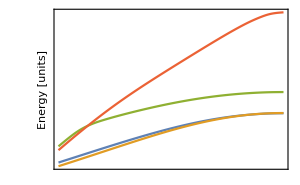

```mathematica
p7 =PlotEnergyFromParameter[data7]
```

```mathematica
Remove[crossingB]
crossingB[d_] := Module[{data, dx1, dx2, i, xs, ys, f1, f2, r,intersections, sortedIndices},
data = d;
Do[
dx1 = data[[i-1,1]]-data[[i-2,1]];
dx2 =data[[i,1]]-data[[i-1,1]];
sortedIndices=Ordering[estimateY[data[[i-2, 2]],data[[i-1,2]],dx1,dx2]];
data[[i,2]][[sortedIndices]]= data[[i,2]],
{i,4,Length[data]}];
xs = First[Transpose[data]];
ys = Transpose[Last[Transpose[data]]];
f1=Interpolation[Transpose[{xs,ys[[1]]}],InterpolationOrder->3];
f2=Interpolation[Transpose[{xs,ys[[2]]}],InterpolationOrder->3];
(*intersections=x/. NSolve[f1[x]==f2[x],{x,First[xs], Last[xs]}];
r = Min[intersections]; But assuming only one root we can simply write:*)
r = x /.FindRoot[f1[x]-f2[x],{x,First[xs],Last[xs]}];
(*Show[ListPlot[Table[Transpose[{xs, ys[[i]]}],{i, Length[ys]}], Joined->False, InterpolationOrder->1, PlotRange->All]];*)
Return[r]]
```

```mathematica
Remove[EnergyDelta]
EnergyDelta[B_,a_:0.3,b_:2,shift_:-1500] := Module[{d}, d=Chop[First[fEEsol[B,{1,1},a,b,shift, 2]]]; Return[Abs[d[[1]] - d[[2]]]]]
```

```mathematica
Remove[EnDeMin]
EnDeMin[B_,a_:0.3,b_:2,shift_:-1500] := Module[{d}, d=Sort[Chop[First[fEEsol[B,{1,1},a,b,shift, 2]]]]; Return[{Abs[d[[2]] - d[[1]]],d[[1]]}]]
```

```mathematica
linecross[x1_,x2_,y11_,y12_,y21_,y22_] := Module[{m1,m2,b1,b2},
m1=(y22-y11)/(x2-x1);
m2=(y21-y12)/(x2-x1);
b1=y11-m1 x1;
b2=y12-m2 x1;
Return[(b2-b1)/(m1-m2)];]
```

```mathematica
Remove[BracketLowerer]
```

```mathematica
BracketLowerer[a_,b_,shift_,inx1_, inx2_,inx4_, iny1_, iny2_,iny4_, precision_] := Module[{x1,x2,x3,x4,y1,y2,y3,y4, l, ratio,e1, e4,sh,sh1,sh2,sh3,sh4,reqDiff,currDiff,i,maxiter},
x1 = inx1;
x4 = inx4;
x2 = inx2;
y1 = iny1;
y4 = iny4;
y2 = iny2;
ratio = 3/2 - Sqrt[5]/2;
l = x4-x1;
x3 = x4 - l*ratio;
{y3,sh3} = EnDeMin[x3, a, b, shift];

(*passing the information of the lowest point (in terms of Energy, not En Delta*)
sh=shift;
sh1=shift;
sh4 = shift;
sh2= shift;

reqDiff=5;
currDiff=reqDiff*2;
i=0;
maxiter=15;
While[And[Or[x4-x1>precision,currDiff>reqDiff],i<maxiter],
(*Print[{x1,x2,x3,x4}];*)
If[y2>y3,
x1=x2;
x2=x3;
x3 = x4 - (x2-x1);

y1=y2;
y2 = y3;

sh1=sh2;
sh2=sh3;

{y3,sh3} = EnDeMin[x3, a, b, sh];,
currDiff=y3;
(*else*)

x4=x3;
x3=x2;
x2 = x1 + (x4-x3);

y4=y3;
y3 = y2;

sh4 = sh3;
sh3=sh2;

{y2,sh2} = EnDeMin[x2, a, b, sh];
currDiff=y2;
];
sh = Min[sh1,sh2,sh3,sh4]*1.02;
i = i+1;
];
(*Return [(x2+x3)/2]*)
(*albo lepiej - można obliczyć punkty (energie) w x1 i x4 i poprowadzić dwie proste
To pozwala na dokładniejszy wynik przy gorszej precyzji -> szybciej*)
If[y2>y3,
x1=x2;,
(*else*)
x4=x3;
];
If[i==maxiter,Return[-currDiff];];
e1 = Chop[First[Transpose[Sort[Transpose[fEEsol[x1,{1,1},a,b,GuessShift[x1,a], 2]]]]]];
e4= Chop[First[Transpose[Sort[Transpose[fEEsol[x4,{1,1},a,b,GuessShift[x4,a], 2]]]]]];
Return[linecross[x1,x4,e1[[1]],e1[[2]],e4[[1]],e4[[2]]]]

]
```

```mathematica
Remove[FindBCrossing]
FindBCrossing[a_:0.3,b_:2] := Module[{y1, y2, y4,x1, x2,x4,result, step, precision,sh},
x1 = 0;
y1 = EnergyDelta[x1, a, b, GuessShift[0,a]];
step = 1;
x2 = step;
y2 = EnergyDelta[x2, a, b, GuessShift[x2,a]];
step = step*GoldenRatio;
x4 = x2+step;
{y4,sh} = EnDeMin[x4, a, b, GuessShift[x4,a]];
While [y2 > y4,
x1 = x2;
y1 = y2;
x2 = x4;
y2 = y4;
step = step*GoldenRatio;
x4=x4+step;
{y4,sh} = EnDeMin[x4, a, b, GuessShift[x4, a]];];
precision=(x1+x4)/2*0.15;
(*after this we know the anwser is between left and right*)
result = BracketLowerer[a,b,sh, x1,x2,x4,y1,y2,y4, precision];
Return[Re[result]]]
```

```mathematica
PlotFromky[ky_,Bmax_,a_,b_,numi_]:=Module[{data,plotted},
data =Table[{B, Chop[First[Transpose[Sort[Transpose[fsol[B,0,-Abs[ky],a,b,GuessShift[B,a],numi]]]]]]},{B,0,Bmax, Bmax/10} ];
plotted = PlotEnergyFromParameter[data];
Return[plotted]]
```

```mathematica
PlotFromRotation[B_,ky_,a_,b_,numi_,minang_,maxang_,numang_]:=Module[{ang,angtab,data,row,plotted},
data={};
angtab = Reverse[ Table[ang*Pi/180, {ang, minang, maxang, (maxang-minang)/numang}]];
Do[
ProgressIndicator[i/Length[angtab]];
ang =angtab[[i]];
setangle[ang];
row ={ang*180/Pi, Chop[First[Transpose[Sort[Transpose[fsol[B,0,-Abs[ky],a,b,GuessShift[B,a],numi]]]]]]};
AppendTo[data,row];
(*Print[{{currentAngle,row[[2]]}}];*)
,{i,1,Length[angtab]}];
plotted = PlotEnergyFromParameter[data,True];
Return[plotted]]
```

```mathematica
(*Plot from rotation (B, ky, a, b, liczba stanow, min ,i max kąt, liczba punktów w x -> łącznie numi*numang*)
```

```mathematica
FindCrossfromAngle[ANG_,a_] := Module[{},
setangle[ANG*Pi/180];
Return[FindBCrossing[a,2]]]
```

```mathematica
AnFsol[ANG_, B_,kx_,ky_,a_:1,b_:1,shift_, numi_ : 12]:=Module[{},
setangle[ANG*Pi/180];
fsol[B,kx,ky,a,b,shift, numi]]
```

```mathematica
corFun[G1_,G2_] := Abs[Correlation[Flatten[G1],Flatten[G2]]]
```

```mathematica
(*Input is a series of matrices and output the ordering (sortedIndices) which maximizes correlation between corresponding matrices
Warning: this is O(m!)*)
Remove[IdxFromGrids]
IdxFromGrids[oldGrids_, newGrids_] := Module[{m ,N, corrMatrix,zerMatrix, asign},
m = Length[oldGrids];
N = Length[oldGrids[[1]]];
corrMatrix = Table[corFun[G1,G2],{G1, oldGrids},{G2,newGrids}];
zerMatrix = Join[Transpose[Join[Table[0,{m},{m}],Transpose[corrMatrix]]],Table[0,{m},{2 m}]];
asign = Cases[FindIndependentEdgeSet[WeightedAdjacencyGraph[zerMatrix]],DirectedEdge[i_,j_]:>{i,j-m}];
Return[Transpose[asign][[2]]];]
```

```mathematica
Remove[PlotEnergyFromWAVE]
(*Takes in { {Bvalue, {{Energies},{{f1x, f1y, f1z},...}} , ...}
so d[[ B number, 1 or 2: B or other, 1 or 2: Energies or WaveF, Lvl num,  1-2-3 : x-y-z]]*)
PlotEnergyFromWAVE[d_,join_ : True, Ngrid_ : 10, intpol_ : 3] := Module[{data, oldGrids,newGrids, i, xs,ys,plotted,sortedIndices},
data = d;
oldGrids = Table[Table [Evaluate[#[Sequence@@{x,y}]&]/@F,{x,-nxr,nxr,nxr*2/Ngrid},{y,-nyr,nyr,nyr*2/Ngrid}],{F,data[[1,2,2]]}];
Do[
newGrids = Table[Table [Evaluate[#[Sequence@@{x,y}]&]/@F,{x,-nxr,nxr,nxr*2/Ngrid},{y,-nyr,nyr,nyr*2/Ngrid}],{F,data[[i,2,2]]}];

sortedIndices=IdxFromGrids[oldGrids,newGrids];
data[[i,2,1]]= data[[i,2,1]][[sortedIndices]];
data[[i,2,2]]= data[[i,2,2]][[sortedIndices]];
oldGrids = newGrids[[sortedIndices]],
{i,2,Length[data]}];
xs = First[Transpose[data]];
ys = Transpose[First[Transpose[Last[Transpose[data]]]]];
plotted=ListPlot[Table[Transpose[{xs, ys[[i]]}],{i, Length[ys]}], Joined->join, InterpolationOrder->intpol, PlotRange->All, ImageSize->Large];
Return[plotted]]
```

```mathematica
newvscalar[x_,y_, a_ : 40] := vscalar[x,y] + a(((x-nxr)/nxr)^4 +((y-nyr)/nyr)^4)
quadV  := newvscalar[x,y]
```

```mathematica
f22Qsol[B_,a_:1,b_:1,shift_,d_,numi_:12]:=NDEigensystem[{
({
-1/2 Laplacian[ψ1[x,y],{x,y}],
-1/2 Laplacian[ψ2[x,y],{x,y}],
-1/2 Laplacian[ψ3[x,y],{x,y}]
}
+(a^2 (IdentityMatrix[3]quadV-b Bx Fx-b By Fy)-B Fz).{ψ1[x,y],ψ2[x,y], ψ3[x,y]}),
DirichletCondition[{ψ1[x,y]==0,ψ2[x,y]==0, ψ3[x, y] == 0},True]},
{ψ1,ψ2, ψ3},{x,-(1+d)nxr,+(2 *2-1 + d) nxr},{y,-(1+d)nyr,+(2 *2-1 + d) nyr},
numi,
Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.002}}},"Eigensystem"->{"Arnoldi","Shift"->shift,"Criteria"->"RealPart",MaxIterations->10000}}];
```

```mathematica
avgabs[F_,left_,right_,Ngrid_:10]:=Mean[Flatten[Abs[Table [Evaluate[#[Sequence@@{x,y}]&]/@F,{x,left nxr,right nxr,nxr (right - left)/Ngrid},{y,left nyr,right nyr,nyr(right - left)/Ngrid}]],1]]
```

```mathematica
wavePlot [ f_,left_,right_]:= Module[{myF,avs},
myF [z_,i_] := f[[i]][Re[z],Im[z]];
avs = avgabs[f,left,right,20];
Transpose[{Table[ComplexPlot[myF[z,i], {z, left(nxr +nyr I), right(nxr+nyr I)}, ColorFunction->{"CyclicArg", "GlobalAbs"}],{i,1,3}],
avs}]]
```

```mathematica
setangle[90*Pi/180]
```

```mathematica
{xn, yn} = {1,1}
currentAngle
```

{1,1}

π/2

```mathematica
FindBCrossing[0.15]
FindBCrossing[0.3]
FindBCrossing[0.5]
```

5.81308

36.0035

113.975

```mathematica
setangle[60*Pi/180]
```

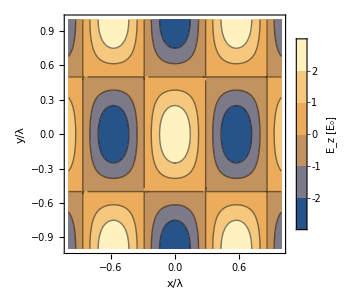

```mathematica
p1 =ContourPlot[Evec[x,y,0][[3]], {x,-xr*2,xr*2},{y,-yr*2,yr*2},
FrameLabel->{Style["x/λ",FontSize->17],Style["y/λ",FontSize->17]}, LabelStyle -> Black,
PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->250,LegendLabel->Style["E_z [E_0]",FontSize->16,Black,Bold]],{After,Top}],ImageSize->300]
```

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\licencjat\\latex\\earlyjpg\\L3\\60Evec.png",p1,ImageResolution->200]
```

C:\Users\kamil\OneDrive\Documents\licencjat\latex\earlyjpg\L3\60Evec.png

```mathematica
p2 = Show@ContourPlot[vscalar[x,y], {x,-2yr,2yr}, {y,-2yr,2yr},
ColorFunction->"BlueGreenYellow",
FrameLabel->{Style["x/λ",FontSize->17],Style["y/λ",FontSize->17]}, LabelStyle -> Black,
PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->250,LegendLabel->Style["V[ℰ_0]",FontSize->16,Black,Bold]],{After,Top}],ImageSize->300]
```

-Graphics-

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\licencjat\\latex\\earlyjpg\\L3\\60vscalar-empty.png",p2,ImageResolution->200]
```

C:\Users\kamil\OneDrive\Documents\licencjat\latex\earlyjpg\L3\60vscalar-empty.png

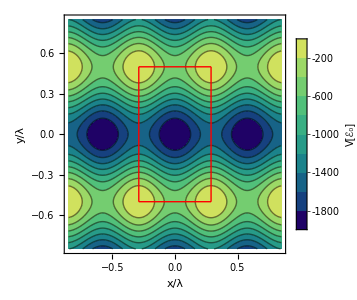

```mathematica
p3 = Show@ContourPlot[vscalar[x,y], {x,-1.7nyr,1.7nyr}, {y,-1.7nyr,1.7nyr},
ColorFunction->"BlueGreenYellow",
FrameLabel->{Style["x/λ",FontSize->13],Style["y/λ",FontSize->13]}, LabelStyle -> Black,
PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->250,LegendLabel->Style["V[ℰ_0]",FontSize->14,Black,Bold]],{After,Top}],
Epilog->{
Red,Thick,Line[{{-nxr,-nyr},{-nxr,nyr}}], Line[{{-nxr,-nyr},{nxr,-nyr}}], Line[{{nxr,nyr},{-nxr,nyr}}], Line[{{nxr,nyr},{nxr,-nyr}}]},ImageSize->300]
```

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\licencjat\\latex\\earlyjpg\\L3\\60vscal2D-EE-showcase.png",p3,ImageResolution->200]
```

C:\Users\kamil\OneDrive\Documents\licencjat\latex\earlyjpg\L3\60vscal2D-EE-showcase.png

```mathematica
setangle[60Degree];
p4 = ContourPlot[vscalar[x,y], {x,-2xr,2xr}, {y,-2yr,2yr},ColorFunction->"BlueGreenYellow",
FrameLabel->{Style["x/λ",FontSize->17],Style["y/λ",FontSize->17]}, LabelStyle -> Black,
(*PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->250,LegendLabel->Style["V(units)",FontSize->16,Black,Bold]],{After,Top}],*)Epilog->{

Red,InfiniteLine[{0, nyr},{1,0}], InfiniteLine[{0, -nyr},{1,0}], InfiniteLine[{nxr, 0},{0,1}], InfiniteLine[{-nxr,0},{0,1}],InfiniteLine[{3nxr, 0},{0,1}], InfiniteLine[{-3nxr,0},{0,1}]}]
```

-Graphics-

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\licencjat\\latex\\earlyjpg\\L3\\60vscal2D-PER.png",p4,ImageResolution->200]
```

C:\Users\kamil\OneDrive\Documents\licencjat\latex\earlyjpg\L3\60vscal2D-PER.png

```mathematica
setangle[75Degree];
p5 = ContourPlot[vscalar[x,y], {x,-2xr,2xr}, {y,-2yr,2yr},ColorFunction->"BlueGreenYellow",
FrameLabel->{Style["x/λ",FontSize->17],Style["y/λ",FontSize->17]}, LabelStyle -> Black,
(*PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->250,LegendLabel->Style["V(units)",FontSize->16,Black,Bold]],{After,Top}],*)Epilog->{

Red,InfiniteLine[{0, nyr},{1,0}], InfiniteLine[{0, -nyr},{1,0}], InfiniteLine[{nxr, 0},{0,1}], InfiniteLine[{-nxr,0},{0,1}],InfiniteLine[{3nxr, 0},{0,1}], InfiniteLine[{-3nxr,0},{0,1}]}]
```

-Graphics-

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\licencjat\\latex\\earlyjpg\\L3\\75vscal2D-PER.png",p5,ImageResolution->200]
```

C:\Users\kamil\OneDrive\Documents\licencjat\latex\earlyjpg\L3\75vscal2D-PER.png

```mathematica
setangle[85Degree];
p6 = ContourPlot[vscalar[x,y], {x,-2xr,2xr}, {y,-2yr,2yr},ColorFunction->"BlueGreenYellow",
FrameLabel->{Style["x/λ",FontSize->17],Style["y/λ",FontSize->17]}, LabelStyle -> Black,
(*PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->250,LegendLabel->Style["V(units)",FontSize->16,Black,Bold]],{After,Top}],*)Epilog->{

Red,InfiniteLine[{0, nyr},{1,0}], InfiniteLine[{0, -nyr},{1,0}], InfiniteLine[{nxr, 0},{0,1}], InfiniteLine[{-nxr,0},{0,1}] }]
```

-Graphics-

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\licencjat\\latex\\earlyjpg\\L3\\85vscal2D-PER.png",p6,ImageResolution->200]
```

C:\Users\kamil\OneDrive\Documents\licencjat\latex\earlyjpg\L3\85vscal2D-PER.png

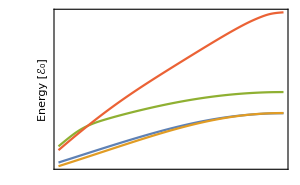

```mathematica
p7 =PlotEnergyFromParameter[data7]
```

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\licencjat\\latex\\earlyjpg\\L3\\bcrit015.pdf",p7]
```

C:\Users\kamil\OneDrive\Documents\licencjat\latex\earlyjpg\L3\bcrit015.pdf

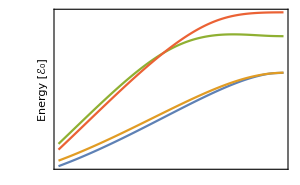

```mathematica
p8=PlotEnergyFromParameter[data8]
```

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\licencjat\\latex\\earlyjpg\\L3\\bcrit03.pdf",p8]
```

C:\Users\kamil\OneDrive\Documents\licencjat\latex\earlyjpg\L3\bcrit03.pdf

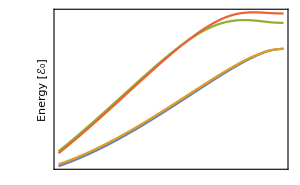

```mathematica
p9 =PlotEnergyFromParameter[data9]
```

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\licencjat\\latex\\earlyjpg\\L3\\bcrit05.pdf",p9]
```

C:\Users\kamil\OneDrive\Documents\licencjat\latex\earlyjpg\L3\bcrit05.pdf

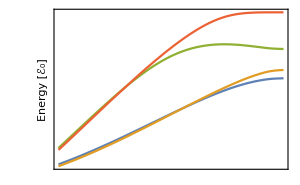

```mathematica
p10 =PlotEnergyFromParameter[data10]
```

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\licencjat\\latex\\earlyjpg\\L3\\krecenie-b20a03.pdf",p10]
```

C:\Users\kamil\OneDrive\Documents\licencjat\latex\earlyjpg\L3\krecenie-b20a03.pdf

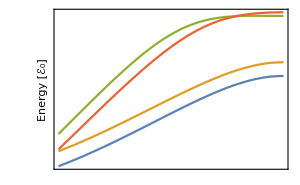

```mathematica
p11 =PlotEnergyFromParameter[data11]
```

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\licencjat\\latex\\earlyjpg\\L3\\krecenie-b60a03.pdf",p11]
```

C:\Users\kamil\OneDrive\Documents\licencjat\latex\earlyjpg\L3\krecenie-b60a03.pdf

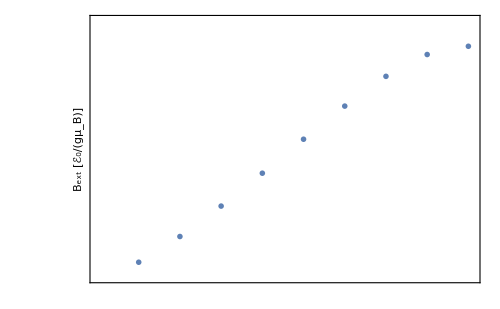

```mathematica
angtable = {10,20,30,40,50,60,70,80,90};
degreeTicks=Table[If[Mod[i+10,20]==0,{i ,i °,0.015},{i,"",0.01}],{i,0,90,5}];
botdegreeTicks = Table[If[Mod[i,20]==0,{i ,"",0.015},{i,"",0.01}],{i,0,90,5}];
p12 =ListPlot[cdata,Joined->False,PlotMarkers->Red,
ImageSize->500,PlotRange->{{0,91},{0,40}},
Frame->True,FrameLabel->{{Style["B_ext [ℰ_0/(gμ_B)]",FontSize->16],None},{None,Style["Lattice angle α",FontSize->16]}}, 
FrameTicks->{{None, All},{botdegreeTicks,degreeTicks}},PlotRangePadding->{{0,0.001},{Automatic,Automatic}},
LabelStyle->{Black,FontSize->13}]
```

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\licencjat\\latex\\earlyjpg\\L3\\anglecross03.pdf",p12]
```

C:\Users\kamil\OneDrive\Documents\licencjat\latex\earlyjpg\L3\anglecross03.pdf

```mathematica
p7 = Show[PlotFromRotation[4.4,0,0.15,2,4,10,90,20]]
```

```mathematica
p8 = Show[PlotFromRotation[34.8,0,0.3,2,4,10,90,20]]
```

```mathematica
p9 = Show[PlotFromRotation[114,0,0.5,2,4,10,90,20]]
```

```mathematica
d000k90 = ParallelTable[{B, Chop[Transpose[Take[Sort[Transpose[fsol[B,0,0,0.15,2,GuessShift[B,0.15],2]]],2]]]},{B,4,6, 0.2} ];
```

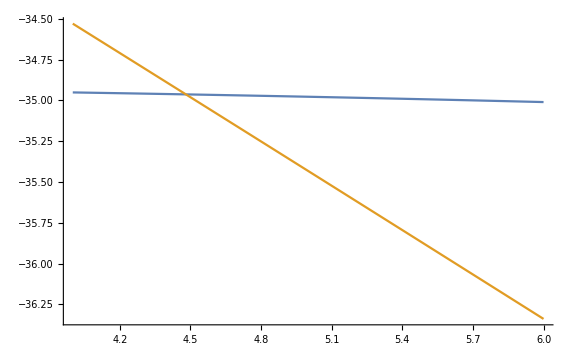

```mathematica
PlotEnergyFromWAVE[d000k90, True,10, 3]
```

```mathematica
currentAngle
```

π/2

```mathematica
angtable = {10,20,30,40,50,60,70,80,90}
```

{10,20,30,40,50,60,70,80,90}

```mathematica
crossTable = ParallelMap[FindCrossfromAngle[#,0.3]&,angtable]
```

{2.39219,6.39398,11.1298,16.2471,21.535,26.691,31.3225,34.7202,36.0035}

```mathematica
deltaE = Table[Sort[Chop[First[AnFsol[angtable[[i]],crossTable[[i]],0,0,0.3,2,GuessShift[117,0.3],2]]]],{i,1,9}]
```

$Aborted

{{10,2.39219},{20,6.39398},{30,11.1298},{40,16.2471},{50,21.535},{60,26.691},{70,31.3225},{80,34.7202},{90,36.0035}}

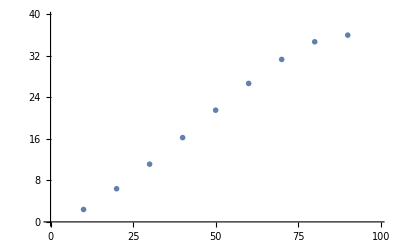

```mathematica
cdata = Transpose[{angtable,crossTable}]
Export["D:\\Licencjat-data\\krecenie-cdata.wl",cdata];
pp1 = ListPlot[cdata,Joined->False,PlotRange->{{0,Last[angtable]*1.1},{0,Last[crossTable]*1.1}},PlotMarkers->Red]
```

```mathematica
p10 = Show[PlotFromRotation[20,0,0.3,2,4,10,90,20]]
```

Show::gtype: Removed[PlotEnergyFromParameter] is not a type of graphics.

Show[Removed[PlotEnergyFromParameter][{{90,{-202.895,-195.988,-178.62,-148.217}},{86,{-203.308,-196.776,-178.215,-148.218}},{82,{-204.52,-198.911,-177.228,-148.279}},{78,{-206.462,-201.974,-176.1,-148.604}},{74,{-209.038,-205.637,-175.185,-149.52}},{70,{-212.143,-209.702,-174.728,-151.422}},{66,{-215.674,-214.044,-174.905,-154.58}},{62,{-219.538,-218.578,-175.867,-158.987}},{58,{-223.653,-223.24,-177.741,-164.45}},{54,{-227.983,-227.952,-180.632,-170.749}},{50,{-232.764,-232.373,-184.592,-177.703}},{46,{-237.544,-236.864,-189.605,-185.174}},{42,{-242.288,-241.377,-195.577,-193.051}},{38,{-246.97,-245.876,-202.368,-201.253}},{34,{-251.559,-250.323,-209.813,-209.703}},{30,{-256.029,-254.683,-218.334,-217.752}},{26,{-260.353,-258.928,-227.087,-226.047}},{22,{-264.51,-263.029,-235.908,-234.58}},{18,{-268.478,-266.962,-244.746,-243.252}},{14,{-272.235,-270.701,-253.553,-251.98}},{10,{-275.764,-274.226,-262.282,-260.689}}},True]]

```mathematica
p11 = Show[PlotFromRotation[60,0,0.3,2,4,10,90,20]]
```

Show::gtype: Removed[PlotEnergyFromParameter] is not a type of graphics.

Show[Removed[PlotEnergyFromParameter][{{90,{-222.83,-212.22,-176.41,-173.622}},{86,{-223.238,-212.613,-176.383,-173.746}},{82,{-224.434,-213.766,-176.327,-174.15}},{78,{-226.349,-215.614,-176.336,-174.939}},{74,{-228.888,-218.065,-176.537,-176.256}},{70,{-231.946,-221.021,-178.248,-177.093}},{66,{-235.422,-224.387,-181.03,-178.173}},{62,{-239.224,-228.075,-184.665,-179.953}},{58,{-243.27,-232.01,-189.152,-182.585}},{54,{-247.495,-236.129,-194.44,-186.175}},{50,{-251.837,-240.376,-200.443,-190.748}},{46,{-256.245,-244.7,-207.057,-196.248}},{42,{-260.67,-249.054,-214.18,-202.561}},{38,{-265.077,-253.405,-221.716,-209.554}},{34,{-269.425,-257.716,-229.577,-217.089}},{30,{-273.683,-261.954,-237.683,-225.039}},{26,{-277.821,-266.089,-245.965,-233.295}},{22,{-281.811,-270.094,-254.358,-241.762}},{18,{-285.629,-273.943,-262.804,-250.357}},{14,{-289.252,-277.616,-271.247,-259.014}},{10,{-292.658,-281.116,-279.611,-267.779}}},True]]

```mathematica
DataFromRotation[B_,ky_,a_,b_,numi_,minang_,maxang_,numang_]:=Module[{ang,angtab,data,row,plotted},
data={};
angtab = Reverse[ Table[ang*Pi/180, {ang, minang, maxang, (maxang-minang)/numang}]];
Do[
ProgressIndicator[i/Length[angtab]];
ang =angtab[[i]];
setangle[ang];
row ={ang*180/Pi, Chop[First[Transpose[Sort[Transpose[fsol[B,0,-Abs[ky],a,b,GuessShift[B,a],numi]]]]]]};
AppendTo[data,row];
(*Print[{{currentAngle,row[[2]]}}];*)
,{i,1,Length[angtab]}];
Return[data]]
```

```mathematica
data7 = DataFromRotation[4.4,0,0.15,2,4,10,90,20];
Export["D:\\Licencjat-data\\krecenie-data7.wl",data7];
```

```mathematica
data8 = DataFromRotation[34.8,0,0.3,2,4,10,90,20];
Export["D:\\Licencjat-data\\krecenie-data8.wl",data8];
```

```mathematica
data9 = DataFromRotation[114,0,0.5,2,4,10,90,20];
Export["D:\\Licencjat-data\\krecenie-data9.wl",data9];
```

```mathematica
data10 = DataFromRotation[20,0,0.3,2,4,10,90,20];
Export["D:\\Licencjat-data\\krecenie-data10.wl",data10];
```

```mathematica
data11 = DataFromRotation[60,0,0.3,2,4,10,90,20];
Export["D:\\Licencjat-data\\krecenie-data11.wl",data11];
```

```mathematica
dtable ={{4.4,0,0.15,2,4,10,90,20},{34.8,0,0.3,2,4,10,90,20},{114,0,0.5,2,4,10,90,20}, {20,0,0.3,2,4,10,90,20},{60,0,0.3,2,4,10,90,20} };
```

```mathematica
{data7, data8, data9, data10, data11} = ParallelTable[DataFromRotation@@ dtable[[i]],{i,5}];
```

```mathematica
Export["D:\\Licencjat-data\\krecenie-data7.wl",data7];
Export["D:\\Licencjat-data\\krecenie-data8.wl",data8];
Export["D:\\Licencjat-data\\krecenie-data9.wl",data9];
Export["D:\\Licencjat-data\\krecenie-data10.wl",data10];
Export["D:\\Licencjat-data\\krecenie-data11.wl",data11];
```

```mathematica
data7 = Import["D:\\Licencjat-data\\krecenie-data7.wl"];
data8 = Import["D:\\Licencjat-data\\krecenie-data8.wl"];
data9 = Import["D:\\Licencjat-data\\krecenie-data9.wl"];
data10 = Import["D:\\Licencjat-data\\krecenie-data10.wl"];
data11 = Import["D:\\Licencjat-data\\krecenie-data11.wl"];
cdata=Import["D:\\Licencjat-data\\krecenie-cdata.wl"];
```

```mathematica
setangle[85Degree];
p13 = StreamPlot[bvector[x,y][[1;;2]],{x,-1.25nyr,1.25nyr},{y,-1.25nyr,1.25nyr},StreamColorFunction->ColorData["BlueGreenYellow"], Prolog->{Black,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}, ImageSize->350,PlotRangePadding->0.015,FrameLabel->{Style["x/λ",FontSize->17],Style["y/λ",FontSize->17]}, LabelStyle -> Black,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->250,LegendLabel->Style["|B_fic| [ℰ_0/gμ_B]",FontSize->16,Black,Bold]],{After,Top}],
Epilog->{Red,Opacity[0.6],InfiniteLine[{0, nyr},{1,0}], InfiniteLine[{0, -nyr},{1,0}], InfiniteLine[{nxr, 0},{0,1}], InfiniteLine[{-nxr,0},{0,1}]}]
```

-Graphics-

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\licencjat\\latex\\earlyjpg\\L3\\85bfic.pdf",p13]
```

C:\Users\kamil\OneDrive\Documents\licencjat\latex\earlyjpg\L3\85bfic.pdf

```mathematica
setangle[75Degree];
p14 = StreamPlot[bvector[x,y][[1;;2]],{x,-1.25nyr,1.25nyr},{y,-1.25nyr,1.25nyr},StreamColorFunction->ColorData["BlueGreenYellow"], Prolog->{Black,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}, ImageSize->350,PlotRangePadding->0.015,FrameLabel->{Style["x/λ",FontSize->17],Style["y/λ",FontSize->17]}, LabelStyle -> Black,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->250,LegendLabel->Style["|B_fic| [ℰ_0/gμ_B]",FontSize->16,Black,Bold]],{After,Top}],
Epilog->{Red,Opacity[0.6],InfiniteLine[{0, nyr},{1,0}], InfiniteLine[{0, -nyr},{1,0}], InfiniteLine[{nxr, 0},{0,1}], InfiniteLine[{-nxr,0},{0,1}]}]
```

-Graphics-

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\licencjat\\latex\\earlyjpg\\L3\\75bfic.pdf",p14]
```

C:\Users\kamil\OneDrive\Documents\licencjat\latex\earlyjpg\L3\75bfic.pdf

```mathematica
setangle[60Degree];
p15 = Show@ StreamPlot[bvector[x,y][[1;;2]], {x,-1.2nyr,1.2nyr}, {y,-1.2nyr,1.2nyr},StreamColorFunction->ColorData["BlueGreenYellow"], Prolog->{Black,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}, ImageSize->350,PlotRangePadding->0.015,FrameLabel->{Style["x/λ",FontSize->17],Style["y/λ",FontSize->17]}, LabelStyle -> Black,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->250,LegendLabel->Style["|B_fic| [ℰ_0/gμ_B]",FontSize->16,Black,Bold]],{After,Top}],
Epilog->{
Red,Opacity[0.6],InfiniteLine[{0, nyr},{1,0}], InfiniteLine[{0, -nyr},{1,0}], InfiniteLine[{nxr, 0},{0,1}], InfiniteLine[{-nxr,0},{0,1}],Thick,Line[{{-nxr,-nyr},{-nxr,nyr}}], Line[{{-nxr,-nyr},{nxr,-nyr}}], Line[{{nxr,nyr},{-nxr,nyr}}], Line[{{nxr,nyr},{nxr,-nyr}}],
Opacity[0.9],
Magenta,Line[{{-nxr,0},{nxr,0}}],
Orange,Line[{{0,-nyr},{0,nyr}}]},ImageSize->300]
```

-Graphics-

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\licencjat\\latex\\earlyjpg\\L3\\60bficMarked.pdf",p15]
```

C:\Users\kamil\OneDrive\Documents\licencjat\latex\earlyjpg\L3\60bficMarked.pdf

```mathematica
wall[x_,ymin_, ymax_,dx_, dy_] := Flatten[{HalfLine[{x,ymax},{0,-1}], Table[Line[{{x,ymax - move},{x+dx,ymax-move - dy}}],{move,0,2000,100}]}]
```

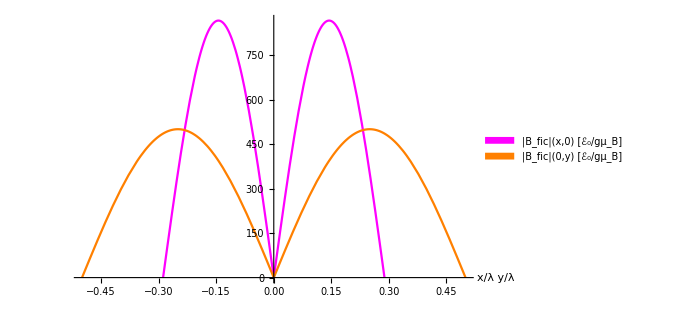

```mathematica
setangle[60Degree];
p16 =Show[{Plot[Norm@bvector[x,0], {x,-nxr,nxr}, PlotStyle->Magenta], Plot[Norm@bvector[0,y], {y,-nyr,nyr}, PlotStyle->Orange]} ,Epilog->{Inset[SwatchLegend[{Magenta,Orange},{"|B_fic|(x,0) [ℰ_0/gμ_B]", "|B_fic|(0,y) [ℰ_0/gμ_B]"},LegendMarkerSize->13,LabelStyle->{FontSize->15}],Scaled[{0.7,0.79}],Left]}, ImageSize->500, PlotRange->All,
AxesLabel->{Style[" x/λ\n y/λ",FontSize->16],None},LabelStyle->Black,AxesStyle->Directive[FontSize->14]]
```

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\licencjat\\latex\\earlyjpg\\L3\\60bfic1D.pdf",p16]
```

C:\Users\kamil\OneDrive\Documents\licencjat\latex\earlyjpg\L3\60bfic1D.pdf

```mathematica
Thick,wall[nxr,-200,Norm@bvector[0,nxr],0.02,100], wall[-nxr,-200,Norm@bvector[0,-nxr],-0.02,100],Red, wall[nyr,-200,1000,0.02,100], wall[-nyr,-200,1000,-0.02,100]
```

```mathematica
setangle[60Degree];
p12 = StreamPlot[bvector[x,y][[1;;2]],{x,-1.25nyr,1.25nyr},{y,-1.25nyr,1.25nyr},StreamColorFunction->ColorData["BlueGreenYellow"], Prolog->{Black,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}, ImageSize->350,PlotRangePadding->0.015,FrameLabel->{Style["x/λ",FontSize->17],Style["y/λ",FontSize->17]}, LabelStyle -> Black,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->250,LegendLabel->Style["|B_fic| [ℰ_0/gμ_B]",FontSize->16,Black,Bold]],{After,Top}],
Epilog->{Red,Opacity[0.6],InfiniteLine[{0, nyr},{1,0}], InfiniteLine[{0, -nyr},{1,0}], InfiniteLine[{nxr, 0},{0,1}], InfiniteLine[{-nxr,0},{0,1}]}]
```

-Graphics-

```mathematica
p15 =Show[{Plot[Norm@bvector[x,0], {x,-nxr,nxr}, PlotStyle->Magenta], Plot[Norm@bvector[0,y], {y,-nyr,nyr}, PlotStyle->Orange]} ,Epilog->{Inset[SwatchLegend[{Magenta,Orange},{"V(r_x,y)[ℰ_0]", "V(x,r_y)[ℰ_0]"},LegendMarkerSize->13,LabelStyle->{FontSize->15}],Scaled[{0.51,0.72}],Left], 
Thick, Magenta,wall[nxr,-2000,vscalar[0,nxr],0.02,100], wall[-nxr,-2000,vscalar[0,-nxr],-0.02,100],Orange, wall[nyr,-2000,vscalar[0,nyr]+200,0.02,100], wall[-nyr,-2000,vscalar[0,-nyr]+200,-0.02,100]}, ImageSize->500, PlotRange->All,
AxesLabel->{Style[" x/λ\n y/λ",FontSize->16],None},LabelStyle->Black]
```

-Graphics-

```mathematica
setangle[90Degree]
```

```mathematica
p15 =Show[{Plot[Norm@bvector[x,0], {x,-nxr,nxr}, PlotStyle->Magenta], Plot[Norm@bvector[y/Sqrt[2],y/Sqrt[2]], {y,-nyr,nyr}, PlotStyle->Orange]} ,Epilog->{Inset[SwatchLegend[{Magenta,Orange},{"V(r_x,y)[ℰ_0]", "V(x,r_y)[ℰ_0]"},LegendMarkerSize->13,LabelStyle->{FontSize->15}],Scaled[{0.51,0.72}],Left], 
Thick, Magenta,wall[nxr,-2000,vscalar[0,nxr],0.02,100], wall[-nxr,-2000,vscalar[0,-nxr],-0.02,100],Orange, wall[nyr,-2000,vscalar[0,nyr]+200,0.02,100], wall[-nyr,-2000,vscalar[0,-nyr]+200,-0.02,100]}, ImageSize->500, PlotRange->All,
AxesLabel->{Style[" x/λ\n y/λ",FontSize->16],None},LabelStyle->Black]
```

-Graphics-

```mathematica
setangle[85Degree];
p15 =Show[{Plot[Norm@bvector[x,0], {x,-nxr,nxr}, PlotStyle->Magenta], Plot[Norm@bvector[0,y], {y,-nyr,nyr}, PlotStyle->Orange]} ,Epilog->{Inset[SwatchLegend[{Magenta,Orange},{"V(r_x,y)[ℰ_0]", "V(x,r_y)[ℰ_0]"},LegendMarkerSize->13,LabelStyle->{FontSize->15}],Scaled[{0.51,0.72}],Left], 
Thick, Magenta,wall[nxr,-2000,vscalar[0,nxr],0.02,100], wall[-nxr,-2000,vscalar[0,-nxr],-0.02,100],Orange, wall[nyr,-2000,vscalar[0,nyr]+200,0.02,100], wall[-nyr,-2000,vscalar[0,-nyr]+200,-0.02,100]}, ImageSize->500, PlotRange->All,
AxesLabel->{Style[" x/λ\n y/λ",FontSize->16],None},LabelStyle->Black]
```

-Graphics-

```mathematica
setangle[75Degree];
p15 =Show[{Plot[Norm@bvector[x,0], {x,-nxr,nxr}, PlotStyle->Magenta], Plot[Norm@bvector[0,y], {y,-nyr,nyr}, PlotStyle->Orange]} ,Epilog->{Inset[SwatchLegend[{Magenta,Orange},{"V(r_x,y)[ℰ_0]", "V(x,r_y)[ℰ_0]"},LegendMarkerSize->13,LabelStyle->{FontSize->15}],Scaled[{0.51,0.72}],Left], 
Thick, Magenta,wall[nxr,-2000,vscalar[0,nxr],0.02,100], wall[-nxr,-2000,vscalar[0,-nxr],-0.02,100],Orange, wall[nyr,-2000,vscalar[0,nyr]+200,0.02,100], wall[-nyr,-2000,vscalar[0,-nyr]+200,-0.02,100]}, ImageSize->500, PlotRange->All,
AxesLabel->{Style[" x/λ\n y/λ",FontSize->16],None},LabelStyle->Black]
```

-Graphics-